```mathematica
Clear["`*"]
```

```mathematica
x1'[t_]=x2[t];
x2'[t_] = 9.8*Sin[x1[t]];
```

```mathematica
p1=D[x1'[t],{t,2}]
```

96.04 Cos[x2[t]] Sin[x2[t]]

```mathematica
FullSimplify[p1]
```

48.02 Sin[2 x2[t]]

```mathematica
p2=D[x2'[t],{t,2}]
p3=D[x2'[t],{t,3}];
p4=D[x2'[t],{t,4}];
p5 =D[x2'[t],{t,5}];
p6 = D[x2'[t],{t,6}];
p7 = D[x2'[t],{t,7}];
p8= D[x2'[t],{t,8}];
p9 = D[x2'[t],{t,9}];
p10= D[x2'[t],{t,10}];
```

-9.8 (96.04 Cos[x2[t]]^2 Sin[x2[t]]-96.04 Sin[x2[t]]^3)

```mathematica
Simplify[p2]
```

-941.192 Cos[x2[t]]^2 Sin[x2[t]]+941.192 Sin[x2[t]]^3

```mathematica
lp1 = 0.33445*x2[t]^2+1.4615*Sin[x1[t]]^2+1.7959*Cos[x1[t]]^2-6.689*Cos[x1[t]]+4.8931
```

4.8931-6.689 Cos[x1[t]]+1.7959 Cos[x1[t]]^2+1.4615 Sin[x1[t]]^2+0.33445 x2[t]^2

```mathematica
D[lp1,t]
```

6.689 Sin[x1[t]] x2[t]-0.6688 Cos[x1[t]] Sin[x1[t]] x2[t]-6.55522 Sin[x2[t]] x2[t]

```mathematica
6.689 Sin[x1[t]] x2[t]-0.6688000000000001 Cos[x1[t]] Sin[x1[t]] x2[t]+0.6689 (-10 Sin[x1[t]]+Cos[x1[t]] Sin[x1[t]]) x2[t]
```

6.689 Sin[x1[t]] x2[t]-0.6688 Cos[x1[t]] Sin[x1[t]] x2[t]+0.6689 (-10 Sin[x1[t]]+Cos[x1[t]] Sin[x1[t]]) x2[t]

```mathematica
Simplify[lp1]
```

6.5218-6.689 Cos[x1[t]]+0.1672 Cos[2 x1[t]]+0.33445 x2[t]^2

```mathematica
n=D[lp3,t]
```

0

```mathematica
FullSimplify[n]
```

0

```mathematica
lp2 = 0.21368*x2[t]^2+1.8731*Sin[x1[t]]^2+2.0867*Cos[x1[t]]^2-4.2736*Cos[x1[t]]+2.1869
```

2.1869-4.2736 Cos[x1[t]]+2.0867 Cos[x1[t]]^2+1.8731 Sin[x1[t]]^2+0.21368 x2[t]^2

```mathematica
lp3 = 2.7309*Sin[x1[t]]^2+2.9258*Cos[x1[t]]^2-3.8215*Cos[x1[t]]+0.19498*x2[t]^2+3.6266
```

3.6266-3.8215 Cos[x1[t]]+2.9258 Cos[x1[t]]^2+2.7309 Sin[x1[t]]^2+0.19498 x2[t]^2

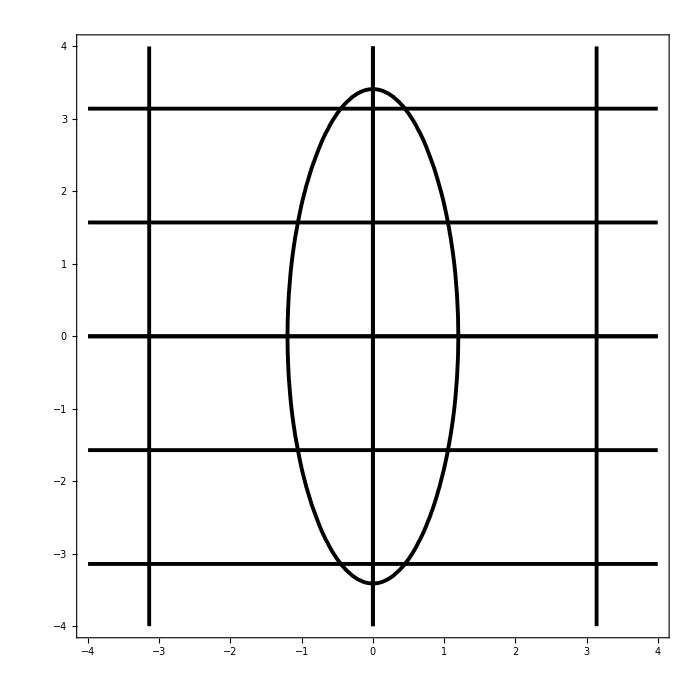

```mathematica
a=ContourPlot[{n==100,p1==0,lp3==5,x1[t]==0,x2[t]==0,Sin[x1[t]]*Cos[x1[t]]- 10Sin[x1[t]]==0},{x1[t],-4,4},{x2[t],-4,4},ContourStyle->Thickness[0.004]]
```

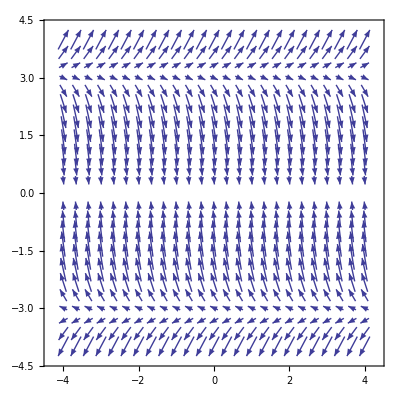

```mathematica
b=VectorPlot[{x1'[t],x2'[t]},{x1[t],-4,4},{x2[t],-4,4},VectorScale->Small,VectorPoints->Fine]
```

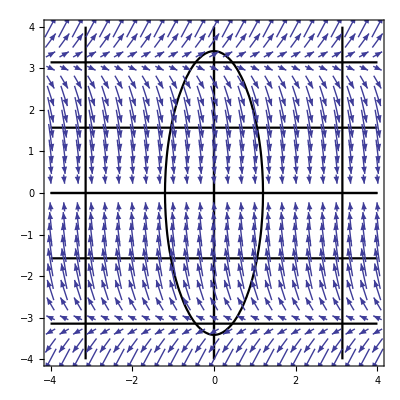

```mathematica
Show[a,b]
```

```mathematica
p1
```

96.04 Cos[x2[t]] Sin[x2[t]]

```mathematica
p2 //TeXForm
```

-9.8 \left(96.04 \sin (\text{x2}(t)) \cos ^2(\text{x2}(t))-96.04 \sin ^3(\text{x2}(t))\right)

```mathematica
Simplify[p4]//TeXForm
```

-451960. \sin ^5(\text{x2}(t))-90392.1 \sin (\text{x2}(t)) \cos ^4(\text{x2}(t))+1.62706\times 10^6 \sin
   ^3(\text{x2}(t)) \cos ^2(\text{x2}(t))

```mathematica
check = -(Sin[x1[t]]*Cos[x1[t]]-10*Sin[x1[t]])*Sin[x1[t]]^2+(Sin[x1[t]]*Cos[x1[t]]-10*Sin[x1[t]])*Cos[x1[t]]^2-10*(Sin[x1[t]]*Cos[x1[t]]-10*Sin[x1[t]])*Cos[x1[t]]-4*x2[t]^2*Sin[x1[t]]*Cos[x1[t]]+10*x2[t]^2*Sin[x1[t]]
```

Sin[x1[t]]^2 (10 Sin[x1[t]]-Cos[x1[t]] Sin[x1[t]])-10 Cos[x1[t]] (-10 Sin[x1[t]]+Cos[x1[t]] Sin[x1[t]])+Cos[x1[t]]^2 (-10 Sin[x1[t]]+Cos[x1[t]] Sin[x1[t]])+10 Sin[x1[t]] x2[t]^2-4 Cos[x1[t]] Sin[x1[t]] x2[t]^2

```mathematica
Plot3D[6.689 Sin[x1[t]] x2[t]-0.6688000000000001 Cos[x1[t]] Sin[x1[t]] x2[t]+0.6689 (-10 Sin[x1[t]]+Cos[x1[t]] Sin[x1[t]]) x2[t],{x1[t],-3,3},{x2[t],-10,10}]
```

-Graphics3D-